## ShowOutwardNormals-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 13:32:12
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
poly={{0,0}, {1,0}, {5,1}, {1, 3}};
```

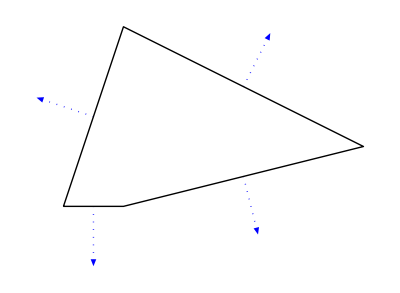

```mathematica
ShowOutwardNormals[poly, {Blue, Dotted, Thick}, True]
```

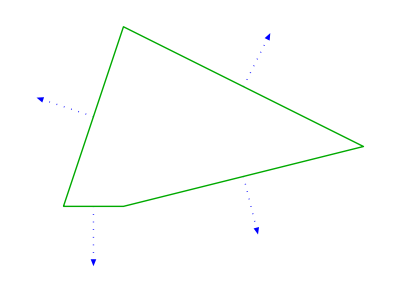

```mathematica
arrows=ShowOutwardNormals[poly, {Blue, Dotted, Thick}, False];
border=Boundary[poly, {Darker[Green], Thick}];
Show[arrows, border]
```

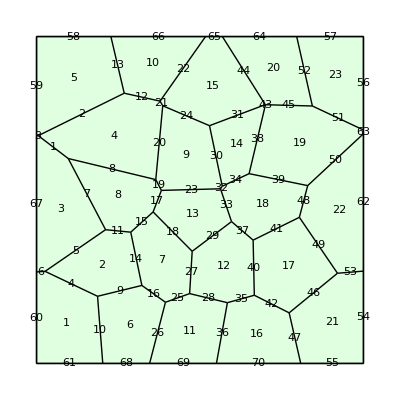

```mathematica
T=TemplateRandomSquareGrid[25,{0,0}, {10,10}];
ShowTissue[T, "CellNumbers"-> True, "EdgeNumbers"-> True]
```

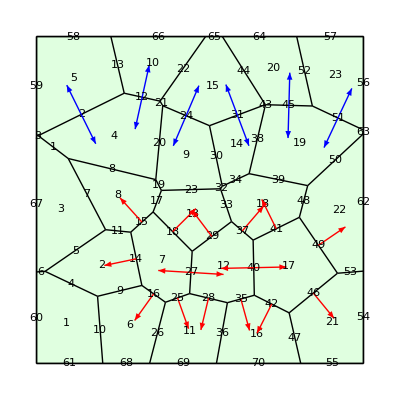

```mathematica
Show[ShowTissue[T, "CellNumbers"-> True, "EdgeNumbers"-> True],

ShowOutwardNormals[T, "Cells"-> {7,12,17}, "Style"-> Red],

ShowOutwardNormals[T, "Edges"-> {2,12,24,31,45,51}, "Style"-> Blue]
]
```